### Expressions for EPR in extrinsically varying cellular populations

```mathematica
EPR = ((ρb-ρu)σb σu)/((σb+σu)(d+σb+σu))Log[ρb/ρu];
```

```mathematica
ExtNoisePdf=FullSimplify[PDF[GammaDistribution[α,1/β],x],x>0]//FullSimplify
```

(ⅇ^(-x β) x^(-1+α) (1/β)^-α)/Gamma[α]

```mathematica
Mean[GammaDistribution[α,1/β]]
```

α/β

```mathematica
Variance[GammaDistribution[α,1/β]]
```

α/β^2

```mathematica
ParsToMoms=Solve[{α/β==m,α/β^2==v},{α,β}][[1]]
```

{α→m^2/v,β→m/v}

```mathematica
Solve[(ρb-ρu)Log[ρb/ρu]==(β Qd Σ(Σ+d))/(σb σu),ρb]//Quiet
```

Solve[(ρb-ρu) Log[ρb/ρu]==(Qd β Σ (d+Σ))/(σb σu),ρb]

```mathematica
Solve[(ρb)Log[ρb/ρu]==(β Qd Σ(Σ+d))/(σb σu),ρb]//FullSimplify//Quiet
```

{{ρb→ⅇ^ProductLog[(Qd β Σ (d+Σ))/(ρu σb σu)] ρu}}

```mathematica
ⅇ^Log[(Qd β Σ (d+Σ))/(ρu σb σu)] ρu
```

(Qd β Σ (d+Σ))/(σb σu)

#### Noise on ρb

```mathematica
expρb=FullSimplify[∫_0^∞ Evaluate[ExtNoisePdf/.x->ρb] EPR ⅆρb,Re[α]>0&&Re[β]>0]
```

(σb σu (1-(α-β ρu) (Log[β]-Log[1/ρu])+(α-β ρu) PolyGamma[0,α]))/(β (σb+σu) (d+σb+σu))

```mathematica
TeXForm[expρb/.{ρb->Subscript[ρ, b],ρu->Subscript[ρ, u],σu->Subscript[σ, u],σb->Subscript[σ, b]}//FullSimplify]
```

\frac{\sigma _b \sigma _u \left(-\left(\left(\alpha -\beta  \rho _u\right) \left(\log (\beta )-\log
   \left(\frac{1}{\rho _u}\right)\right)\right)+\psi ^{(0)}(\alpha ) \left(\alpha -\beta  \rho
   _u\right)+1\right)}{\beta  \left(\sigma _b+\sigma _u\right) \left(\sigma _b+d+\sigma _u\right)}

```mathematica
diffρb=(expρb-EPR)/EPR/.ρb->α/β//FullSimplify
```

(1-(α-β ρu) (Log[β]-Log[1/ρu]+Log[α/(β ρu)])+(α-β ρu) PolyGamma[0,α])/((α-β ρu) Log[α/(β ρu)])

```mathematica
diffρbMoms=diffρb/.ParsToMoms//FullSimplify
```

(v-m (m-ρu) (Log[m/v]-Log[1/ρu]+Log[m/ρu])+m (m-ρu) PolyGamma[0,m^2/v])/(m (m-ρu) Log[m/ρu])

```mathematica
diffρbMomsVeqM=diffρbMoms/.v->m//FullSimplify
```

(1+(m-ρu) (Log[1/ρu]-Log[m/ρu])+(m-ρu) PolyGamma[0,m])/((m-ρu) Log[m/ρu])

```mathematica
diffρbMomsVeqM/.m->10/.ρu->999/100//N
```

99899.2

```mathematica
parsρbChangingρu={
{σb->20,σu->10,ρu->10^-0,d->1,m->10},{σb->20,σu->10,ρu->10^-1,d->1,m->10},{σb->20,σu->10,ρu->10^-2,d->1,m->10}}
```

{{σb→20,σu→10,ρu→1,d→1,m→10},{σb→20,σu→10,ρu→1/10,d→1,m→10},{σb→20,σu→10,ρu→1/100,d→1,m→10}}

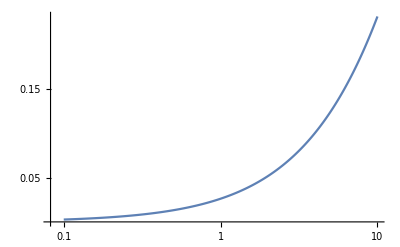

```mathematica
ListPlot[Table[{v/m,diffρbMoms}/.parsρbChangingρu[[1]],{v,1,100,1/10}],PlotRange->All,ScalingFunctions->{"Log","Linear"},Joined->True]
```

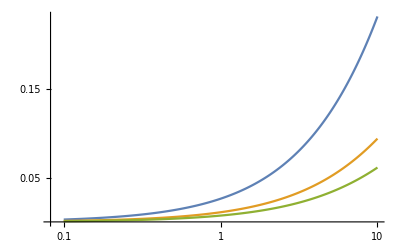

```mathematica
ListPlot[Table[Table[{v/m,diffρbMoms}/.parsρbChangingρu[[i]],{v,1,100,1/10}],{i,1,3}],PlotRange->All,ScalingFunctions->{"Log","Linear"},Joined->True]
```

Note, variation of ρu can have large effects on the effect of extrinsic noise on ρb on the EPR bound. This could provide a potential reason for having genes which switch off. It contrasts against the no extrinsic noise case since there increasing ρu only acts to decrease the EPR. However the difference is not a function of other parameters!

```mathematica
ρuvals = Table[ρu->10^x,{x,-2,0,1/(30)}];
```

```mathematica
mρbvals = Table[m->10^x,{x,1,2,1/30}];
```

```mathematica
dataρumExtρb=Flatten[Table[Table[{ρu,m,diffρbMoms}//.{v->m,ρuvals[[i]],mρbvals[[j]]},{i,1,Length[ρuvals]}],{j,1,Length[mρbvals]}],1];
```

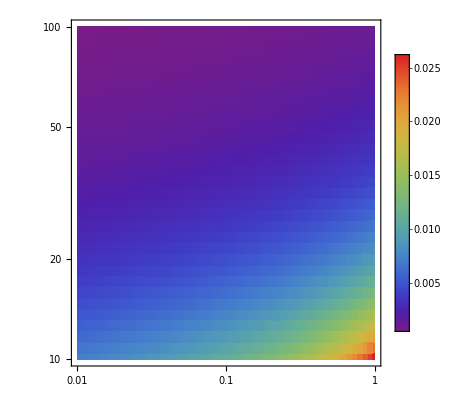

```mathematica
ListDensityPlot[dataρumExtρb,PlotRange->All,ColorFunction->"Rainbow",PlotLegends->BarLegend[{"Rainbow",{Min[dataρumExtρb[[All,3]]],Max[dataρumExtρb[[All,3]]]}}],ScalingFunctions->{"Log","Log"},InterpolationOrder->0]
```

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\ext-plots\\rho_b_hm.csv",dataρumExtρb//N]
```

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\ext-plots\rho_b_hm.csv

```mathematica
{ρbp1,ρbp2,ρbp3}=Table[Table[{v/m,diffρbMoms}/.parsρbChangingρu[[i]]//N,{v,1,100,1/10}],{i,1,3}]
```

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\ext-plots\\rho_b_p1.csv",ρbp1//N]
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\ext-plots\\rho_b_p2.csv",ρbp2//N]
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\ext-plots\\rho_b_p3.csv",ρbp3//N]
```

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\ext-plots\rho_b_p1.csv

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\ext-plots\rho_b_p2.csv

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\ext-plots\rho_b_p3.csv

#### Noise on σu

```mathematica
expσu=FullSimplify[∫_0^∞ Evaluate[ExtNoisePdf/.x->σu] EPR ⅆσu,α>0&&β>0&&ρb>0&&ρu>0&&σb>0&&d>0]
```

1/d ⅇ^(β σb) α (ρb-ρu) σb (ExpIntegralE[1+α,β σb]-ⅇ^(d β) ExpIntegralE[1+α,β (d+σb)]) Log[ρb/ρu]

```mathematica
TeXForm[1/d ⅇ^(β σb) α (ρb-ρu) σb (ExpIntegralE[1+α,β σb]-ⅇ^(d β) ExpIntegralE[1+α,β (d+σb)]) Log[ρb/ρu]/.{ρb->Subscript[ρ, b],ρu->Subscript[ρ, u],σu->Subscript[σ, u],σb->Subscript[σ, b]}//FullSimplify]
```

\frac{\alpha  \sigma _b e^{\beta  \sigma _b} \left(\rho _b-\rho _u\right) \log \left(\frac{\rho
   _b}{\rho _u}\right) \left(E_{\alpha +1}\left(\beta  \sigma _b\right)-e^{\beta  d} E_{\alpha
   +1}\left(\beta  \left(d+\sigma _b\right)\right)\right)}{d}

```mathematica
diffσu=(expσu-EPR)/EPR/.σu->α/β//FullSimplify
```

-1+1/(d β)ⅇ^(β σb) (α+β σb) (α+β (d+σb)) (ExpIntegralE[1+α,β σb]-ⅇ^(d β) ExpIntegralE[1+α,β (d+σb)])

```mathematica
diffσuMoms=diffσu/.ParsToMoms//FullSimplify
```

-1+(ⅇ^((m σb)/v) m (m+σb) (d+m+σb) (ExpIntegralE[(m^2+v)/v,(m σb)/v]-ⅇ^((d m)/v) ExpIntegralE[(m^2+v)/v,(m (d+σb))/v]))/(d v)

This is not a function of ρb or ρu!

```mathematica
parsσu1={σb->10,ρb->20,ρu->0.1,d->1,m->1}
```

{σb→10,ρb→20,ρu→0.1,d→1,m→1}

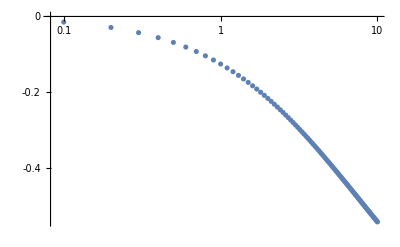

```mathematica
ListPlot[Table[{v/m,diffσuMoms}/.parsσu1,{v,1/10,10,1/10}],PlotRange->All,ScalingFunctions->{"Log","Linear"}]
```

```mathematica
parsσu2={σb->10,ρb->20,ρu->0.1,d->1,m->10}
```

{σb→10,ρb→20,ρu→0.1,d→1,m→10}

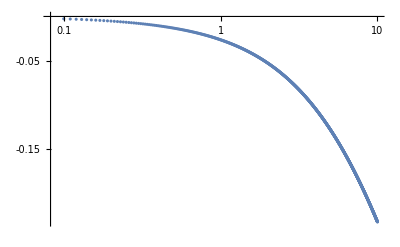

```mathematica
ListPlot[Table[{v/m,diffσuMoms}/.parsσu2,{v,1,100,1/10}],PlotRange->All,ScalingFunctions->{"Log","Linear"}]
```

```mathematica
parsσu3={σb->10,ρb->20,ρu->0.1,d->1,m->100}
```

{σb→10,ρb→20,ρu→0.1,d→1,m→100}

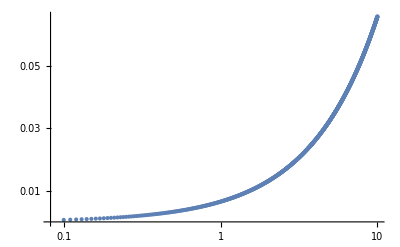

```mathematica
ListPlot[Table[{v/m,diffσuMoms}/.parsσu3,{v,10,1000,1}],PlotRange->All,ScalingFunctions->{"Log","Linear"}]
```

```mathematica
parsσuChangingd={{σb->3,ρb->20,ρu->0.1,d->0.1,m->10},{σb->3,ρb->20,ρu->0.1,d->1,m->10},{σb->3,ρb->20,ρu->0.1,d->10,m->10}}
```

{{σb→3,ρb→20,ρu→0.1,d→0.1,m→10},{σb→3,ρb→20,ρu→0.1,d→1,m→10},{σb→3,ρb→20,ρu→0.1,d→10,m→10}}

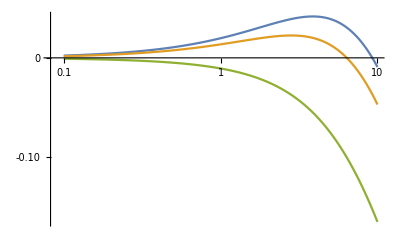

```mathematica
ListPlot[Table[Table[{v/m,diffσuMoms}/.parsσuChangingd[[i]],{v,1,100,1/10}],{i,1,3}],PlotRange->All,ScalingFunctions->{"Log","Linear"},Joined->True]
```

```mathematica
diffσuMoms//.v->1*m//.parsσuChangingσb[[1]]//N
```

0.0529516

Implications for the variation of the burst frequency in the population.

```mathematica
dvals = Table[d->10^x,{x,-1,1,1/(30)}];
```

```mathematica
mσuvals = Table[m->10^x,{x,-2,2,1/(30)}];
```

```mathematica
datadmExtσu=Flatten[Table[Table[{d,m,diffσuMoms}//.{v->m,dvals[[i]],mσuvals[[j]],σb->1},{i,1,Length[dvals]}],{j,1,Length[mσuvals]}],1]//N;
```

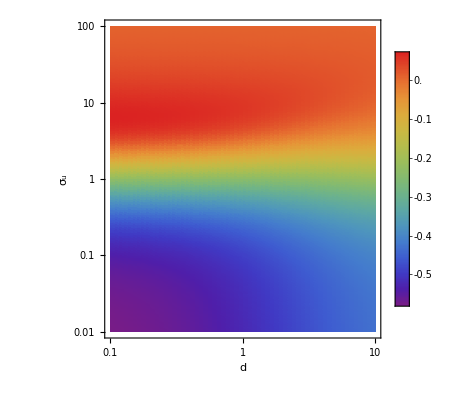

```mathematica
ListDensityPlot[datadmExtσu,PlotRange->All,ColorFunction->"Rainbow",PlotLegends->BarLegend[{"Rainbow",{Min[datadmExtσu[[All,3]]],Max[datadmExtσu[[All,3]]]}}],ScalingFunctions->{"Log","Log"},FrameLabel->{"d","σ_u"}]
```

```mathematica
datadmExtσu2=Flatten[Table[Table[{d,m,diffσuMoms}//.{v->m,dvals[[i]],mσuvals[[j]],σb->100},{i,1,Length[dvals]}],{j,1,Length[mσuvals]}],1]//N;
```

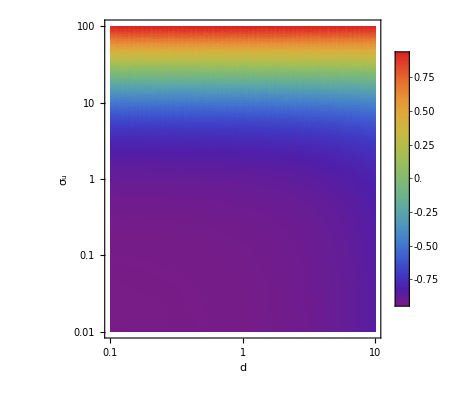

```mathematica
ListDensityPlot[datadmExtσu2,PlotRange->All,ColorFunction->"Rainbow",PlotLegends->BarLegend[{"Rainbow",{Min[datadmExtσu[[All,3]]],Max[datadmExtσu[[All,3]]]}}],ScalingFunctions->{"Log","Log"},FrameLabel->{"d","σ_u"}]
```

```mathematica
Max[datadmExtσu[[All,3]]]
```

0.0657874

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\ext-plots\\sigma_u_hm.csv",datadmExtσu//N]
```

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\ext-plots\sigma_u_hm.csv

```mathematica
Min[{σup1,σup2,σup3}//Flatten]
```

-0.164738

```mathematica
{σup1,σup2,σup3}=Table[Table[{v/m,diffσuMoms}/.parsσuChangingd[[i]],{v,1,100,1/10}],{i,1,3}]//N//Quiet
```

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\ext-plots\\sigma_u_p1.csv",σup1//N]
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\ext-plots\\sigma_u_p2.csv",σup2//N]
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\ext-plots\\sigma_u_p3.csv",σup3//N]
```

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\ext-plots\sigma_u_p1.csv

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\ext-plots\sigma_u_p2.csv

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\ext-plots\sigma_u_p3.csv

#### Noise on d

```mathematica
expd=FullSimplify[∫_0^∞ Evaluate[ExtNoisePdf/.x->d] EPR ⅆd,α>0&&β>0&&ρb>0&&ρu>0&&σb>0&&d>0&&(σu∉Reals&&σu≠Re[σu])||σb+Re[σu]>0]
```

ConditionalExpression[ⅇ^(β (σb+σu)) β^α (ρb-ρu) σb σu (σb+σu)^(-2+α) Gamma[1-α,β (σb+σu)] Log[ρb/ρu], Re[α]>0&&Re[β]>0&&((σu∉ℝ&&Im[σu]≠0)||σb+Re[σu]>0)]

```mathematica
EPR
```

((ρb-ρu) σb σu Log[ρb/ρu])/((σb+σu) (d+σb+σu))

```mathematica
diffd=FullSimplify[(expd-EPR)/EPR/.d->α/β//FullSimplify,σb>0&&σu>0&&Re[α]>0&&Re[β]>0]
```

-1+ⅇ^(β (σb+σu)) (α+β (σb+σu)) ExpIntegralE[α,β (σb+σu)]

```mathematica
TeXForm[-1+ⅇ^(β (σb+σu)) β (m+σb+σu) ExpIntegralE[α,β (σb+σu)]]
```

\beta  e^{\beta  (\text{$\sigma $b}+\text{$\sigma $u})} (m+\text{$\sigma $b}+\text{$\sigma $u})
   E_{\alpha }(\beta  (\text{$\sigma $b}+\text{$\sigma $u}))-1

This is not a function of ρb or ρu!

```mathematica
diffdMoms=diffd/.ParsToMoms//FullSimplify
```

-1+(ⅇ^((m (σb+σu))/v) m (m+σb+σu) ExpIntegralE[m^2/v,(m (σb+σu))/v])/v

```mathematica
parsdChangingσu={{σb->1,ρb->20,ρu->0.1,σu->1,m->1},{σb->1,ρb->20,ρu->0.1,σu->10,m->1},{σb->1,ρb->20,ρu->0.1,σu->100,m->1}}
```

{{σb→1,ρb→20,ρu→0.1,σu→1,m→1},{σb→1,ρb→20,ρu→0.1,σu→10,m→1},{σb→1,ρb→20,ρu→0.1,σu→100,m→1}}

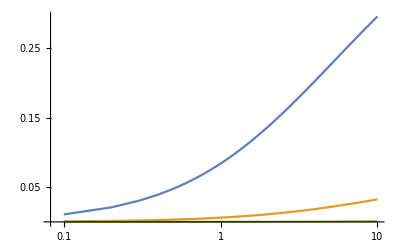

```mathematica
ListPlot[Table[Table[{v/m,diffdMoms}/.parsdChangingσu[[i]],{v,1/10,10,1/10}],{i,1,3}],PlotRange->All,ScalingFunctions->{"Log","Linear"},Joined->True]
```

```mathematica
SetPrecision[Table[{v/m,diffdMoms}/.parsdChangingσu[[3]],{v,1/10,10,1/10}],1000]//N
```

{{0.1,9.59317×10^-6},{0.2,0.0000191495},{0.3,0.0000286694},{0.4,0.000038153},{0.5,0.0000476008},{0.6,0.000057013},{0.7,0.0000663898},{0.8,0.0000757317},{0.9,0.0000850389},{1.,0.0000943116},{1.1,0.00010355},{1.2,0.000112755},{1.3,0.000121926},{1.4,0.000131064},{1.5,0.000140168},{1.6,0.00014924},{1.7,0.00015828},{1.8,0.000167287},{1.9,0.000176262},{2.,0.000185205},{2.1,0.000194117},{2.2,0.000202997},{2.3,0.000211846},{2.4,0.000220665},{2.5,0.000229452},{2.6,0.00023821},{2.7,0.000246937},{2.8,0.000255634},{2.9,0.000264302},{3.,0.00027294},{3.1,0.000281549},{3.2,0.000290129},{3.3,0.000298679},{3.4,0.000307202},{3.5,0.000315695},{3.6,0.000324161},{3.7,0.000332598},{3.8,0.000341008},{3.9,0.00034939},{4.,0.000357744},{4.1,0.000366072},{4.2,0.000374372},{4.3,0.000382645},{4.4,0.000390891},{4.5,0.000399111},{4.6,0.000407305},{4.7,0.000415472},{4.8,0.000423614},{4.9,0.000431729},{5.,0.000439819},{5.1,0.000447884},{5.2,0.000455923},{5.3,0.000463937},{5.4,0.000471926},{5.5,0.00047989},{5.6,0.000487829},{5.7,0.000495744},{5.8,0.000503635},{5.9,0.000511501},{6.,0.000519343},{6.1,0.000527162},{6.2,0.000534956},{6.3,0.000542728},{6.4,0.000550475},{6.5,0.0005582},{6.6,0.000565901},{6.7,0.000573579},{6.8,0.000581234},{6.9,0.000588867},{7.,0.000596477},{7.1,0.000604065},{7.2,0.00061163},{7.3,0.000619173},{7.4,0.000626694},{7.5,0.000634193},{7.6,0.00064167},{7.7,0.000649126},{7.8,0.00065656},{7.9,0.000663973},{8.,0.000671364},{8.1,0.000678734},{8.2,0.000686084},{8.3,0.000693412},{8.4,0.00070072},{8.5,0.000708007},{8.6,0.000715273},{8.7,0.000722519},{8.8,0.000729745},{8.9,0.00073695},{9.,0.000744135},{9.1,0.000751301},{9.2,0.000758446},{9.3,0.000765572},{9.4,0.000772678},{9.5,0.000779765},{9.6,0.000786832},{9.7,0.00079388},{9.8,0.000800909},{9.9,0.000807918},{10.,0.000814909}}

For m=v plot heat map of mean of d vs σb.

```mathematica
σuvals = Table[σu->10^x,{x,-2,2,1/(30)}];
```

```mathematica
mdvals = Table[m->10^x,{x,-1,1,1/(30)}];
```

```mathematica
dataσumExtd=Flatten[Table[Table[{σu,m,diffdMoms}//.{v->m,σuvals[[i]],mdvals[[j]],σb->10},{i,1,Length[σuvals]}],{j,1,Length[mdvals]}],1]//N;
```

```mathematica
dataσumExtd;
```

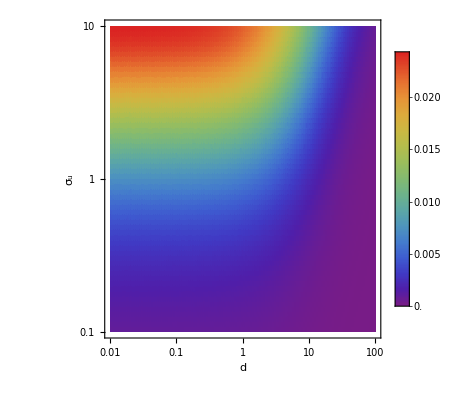

```mathematica
ListDensityPlot[dataσumExtd,PlotRange->All,ColorFunction->"Rainbow",PlotLegends->BarLegend[{"Rainbow",{Min[dataσumExtd[[All,3]]],Max[dataσumExtd[[All,3]]]}}],ScalingFunctions->{"Log","Log"},FrameLabel->{"d","σ_u"}]
```

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\ext-plots\\d_hm.csv",dataσumExtd//N]
```

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\ext-plots\d_hm.csv

```mathematica
Min[{dp1,dp2,dp3}//Flatten]
```

9.59317×10^-6

```mathematica
{dp1,dp2,dp3}=Table[SetPrecision[Table[{v/m,diffdMoms}/.parsdChangingσu[[i]],{v,1/10,10,1/10}],1000],{i,1,3}]//N//Quiet;
```

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\ext-plots\\d_p1.csv",dp1//N]
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\ext-plots\\d_p2.csv",dp2//N]
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\ext-plots\\d_p3.csv",dp3[[1;;]]//N]
```

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\ext-plots\d_p1.csv

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\ext-plots\d_p2.csv

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\ext-plots\d_p3.csv

#### Noise on ρu

```mathematica
expρu=FullSimplify[∫_0^∞ Evaluate[ExtNoisePdf/.x->ρu] EPR ⅆρu,α>0&&β>0&&ρb>0&&ρu>0&&σb>0&&d>0]
```

(σb σu (1+(-α+β ρb) Log[β ρb]+(α-β ρb) PolyGamma[0,α]))/(β (σb+σu) (d+σb+σu))

```mathematica
TeXForm[expρu/.{ρb->Subscript[ρ, b],ρu->Subscript[ρ, u],σu->Subscript[σ, u],σb->Subscript[σ, b]}//FullSimplify]
```

\frac{\sigma _b \sigma _u \left(\left(\beta  \rho _b-\alpha \right) \log \left(\beta  \rho _b\right)+\psi ^{(0)}(\alpha ) \left(\alpha -\beta  \rho _b\right)+1\right)}{\beta  \left(\sigma _b+\sigma _u\right) \left(\sigma
   _b+d+\sigma _u\right)}

```mathematica
diffρu=FullSimplify[(expρu-EPR)/EPR/.ρu->α/β//FullSimplify,σb>0&&σu>0&&Re[α]>0&&Re[β]>0]
```

(-1+(α-β ρb) (Log[β ρb]-Log[(β ρb)/α])+(-α+β ρb) PolyGamma[0,α])/((α-β ρb) Log[(β ρb)/α])

```mathematica
diffρuMoms=diffρu/.ParsToMoms//FullSimplify
```

(-v+m (m-ρb) (-Log[ρb/m]+Log[(m ρb)/v])+m (-m+ρb) PolyGamma[0,m^2/v])/(m (m-ρb) Log[ρb/m])

```mathematica
parsρuChangingσb={{σb->1,ρb->10.1,d->1,σu->10,m->10},{σb->1,ρb->50,d->1,σu->10,m->10},{σb->1,ρb->100,d->1,σu->10,m->10}}
```

{{σb→1,ρb→10.1,d→1,σu→10,m→10},{σb→1,ρb→50,d→1,σu→10,m→10},{σb→1,ρb→100,d→1,σu→10,m→10}}

Variation of parameters in the population

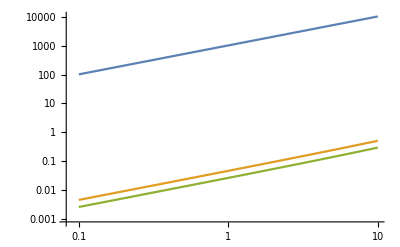

```mathematica
ListPlot[Table[Table[{v/m,diffρuMoms}/.parsρuChangingσb[[i]],{v,1,100,1/10}],{i,1,3}],PlotRange->All,ScalingFunctions->{"Log","Log"},Joined->True]
```

Bigger effect for larger ρu too! Play with this. For m=v plot heat map of mean of ρu vs σb.

```mathematica
ρbvals = Table[ρb->10^x,{x,1001/1000,2,1/(2*11)}];
```

```mathematica
mρuvals = Table[m->10^x,{x,-1,1,1}];
```

```mathematica
dataρbmExtρu=Flatten[Table[Table[{ρb,m,diffρuMoms}//.{v->m,ρbvals[[i]],mρuvals[[j]],σb->1},{i,1,Length[ρbvals]}],{j,1,Length[mρuvals]}],1]//N;
```

```mathematica
dataρbmExtρu
```

{{10.0231,0.1,1.78448},{11.129,0.1,1.7427},{12.3569,0.1,1.70295},{13.7203,0.1,1.66507},{15.2341,0.1,1.62894},{16.915,0.1,1.59442},{18.7814,0.1,1.56141},{20.8536,0.1,1.52981},{23.1546,0.1,1.49952},{25.7093,0.1,1.47046},{28.546,0.1,1.44255},{31.6957,0.1,1.41572},{35.1929,0.1,1.38991},{39.0759,0.1,1.36506},{43.3874,0.1,1.34112},{48.1746,0.1,1.31802},{53.49,0.1,1.29573},{59.3919,0.1,1.27421},{65.945,0.1,1.2534},{73.2211,0.1,1.23329},{81.3001,0.1,1.21382},{90.2704,0.1,1.19497},{10.0231,1.,0.298515},{11.129,1.,0.280526},{12.3569,1.,0.264603},{13.7203,1.,0.250424},{15.2341,1.,0.237731},{16.915,1.,0.22631},{18.7814,1.,0.215985},{20.8536,1.,0.20661},{23.1546,1.,0.198063},{25.7093,1.,0.190241},{28.546,1.,0.183057},{31.6957,1.,0.176436},{35.1929,1.,0.170314},{39.0759,1.,0.164637},{43.3874,1.,0.159358},{48.1746,1.,0.154436},{53.49,1.,0.149835},{59.3919,1.,0.145524},{65.945,1.,0.141475},{73.2211,1.,0.137665},{81.3001,1.,0.134072},{90.2704,1.,0.130678},{10.0231,10.,18861.5},{11.129,10.,8.75613},{12.3569,10.,2.24507},{13.7203,10.,1.01055},{15.2341,10.,0.574612},{16.915,10.,0.371839},{18.7814,10.,0.261328},{20.8536,10.,0.194529},{23.1546,10.,0.151085},{25.7093,10.,0.121246},{28.546,10.,0.0998658},{31.6957,10.,0.0840196},{35.1929,10.,0.0719457},{39.0759,10.,0.0625313},{43.3874,10.,0.0550455},{48.1746,10.,0.0489923},{53.49,10.,0.0440252},{59.3919,10.,0.0398966},{65.945,10.,0.0364256},{73.2211,10.,0.0334773},{81.3001,10.,0.03095},{90.2704,10.,0.0287654}}

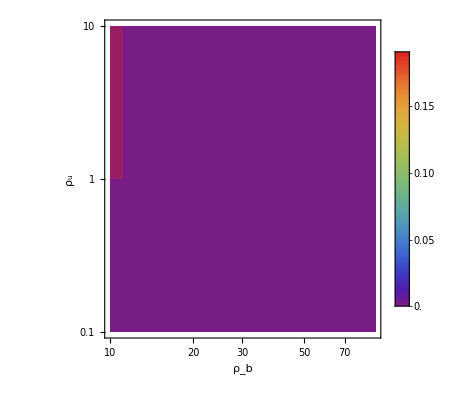

```mathematica
ListDensityPlot[dataρbmExtρu,PlotRange->All,ColorFunction->"Rainbow",PlotLegends->BarLegend[{"Rainbow",{Min[dataσumExtd[[All,3]]],Max[dataσumExtd[[All,3]]]}}],ScalingFunctions->{"Log","Log"},FrameLabel->{"ρ_b","ρ_u"}]
```

### Other stuff

```mathematica
pPDF[n_]:=((ρ/d)^n Exp[-ρ/d])/(n!)
```

```mathematica
Limit[∑_(n=0)^∞ (pPDF[n]r-pPDF[n+1]d(n+1))Log[(pPDF[n]r)/(pPDF[n+1]d(n+1))]//FullSimplify,r->ρ]
```

0

```mathematica
∑_(n=0)^∞ ((ρ/d)^n Exp[-ρ/d])/(n!)Log[((ρ/d)^n Exp[-ρ/d])/(n!)]//FullSimplify
```

∑_(n=0)^∞ (ⅇ^(-ρ/d) (ρ/d)^n Log[(ⅇ^(-ρ/d) (ρ/d)^n)/(n!)])/(n!)

#### Noise on σb

```mathematica
expσu=FullSimplify[∫_0^∞ Evaluate[ExtNoisePdf/.x->σb] EPR ⅆσb,α>0&&β>0&&ρb>0&&ρu>0&&σu>0&&d>0]
```

1/d ⅇ^(β σu) α (ρb-ρu) σu (ExpIntegralE[1+α,β σu]-ⅇ^(d β) ExpIntegralE[1+α,β (d+σu)]) Log[ρb/ρu]

```mathematica
diffσu=(expσu-EPR)/EPR/.σb->α/β//FullSimplify
```

-1+1/(d β)ⅇ^(β σu) (α+β σu) (α+β (d+σu)) (ExpIntegralE[1+α,β σu]-ⅇ^(d β) ExpIntegralE[1+α,β (d+σu)])

```mathematica
diffσuMoms=diffσu/.ParsToMoms//FullSimplify
```

-1+(ⅇ^((m σu)/v) m (m+σu) (d+m+σu) (ExpIntegralE[(m^2+v)/v,(m σu)/v]-ⅇ^((d m)/v) ExpIntegralE[(m^2+v)/v,(m (d+σu))/v]))/(d v)

This is not a function of ρb or ρu!

```mathematica
parsσu1={σu->10,ρb->20,ρu->0.1,d->1,m->1}
```

{σu→10,ρb→20,ρu→0.1,d→1,m→1}

```mathematica
ListPlot[Table[{v/m,diffσuMoms}/.parsσu1,{v,1/10,10,1/10}],PlotRange->All,ScalingFunctions->{"Log","Linear"}]
```

-Graphics-

```mathematica
parsσu2={σu->10,ρb->20,ρu->0.1,d->1,m->10}
```

{σu→10,ρb→20,ρu→0.1,d→1,m→10}

```mathematica
ListPlot[Table[{v/m,diffσuMoms}/.parsσu2,{v,1,100,1/10}],PlotRange->All,ScalingFunctions->{"Log","Linear"}]
```

-Graphics-

```mathematica
parsσu3={σb->10,ρb->20,ρu->0.1,d->1,m->100}
```

{σb→10,ρb→20,ρu→0.1,d→1,m→100}

```mathematica
ListPlot[Table[{v/m,diffσuMoms}/.parsσu3,{v,10,1000,1}],PlotRange->All,ScalingFunctions->{"Log","Linear"}]
```

-Graphics-

```mathematica
parsσuChangingd={{σb->3,ρb->20,ρu->0.1,d->0.1,m->10},{σb->3,ρb->20,ρu->0.1,d->1,m->10},{σb->3,ρb->20,ρu->0.1,d->10,m->10}}
```

{{σb→3,ρb→20,ρu→0.1,d→0.1,m→10},{σb→3,ρb→20,ρu→0.1,d→1,m→10},{σb→3,ρb→20,ρu→0.1,d→10,m→10}}

```mathematica
ListPlot[Table[Table[{v/m,diffσuMoms}/.parsσuChangingd[[i]],{v,1,100,1/10}],{i,1,3}],PlotRange->All,ScalingFunctions->{"Log","Linear"},Joined->True]
```

-Graphics-

```mathematica
diffσuMoms//.v->1*m//.parsσuChangingσb[[1]]//N
```

0.0529516

Implications for the variation of the burst frequency in the population.

```mathematica
dvals = Table[d->10^x,{x,-1,1,1/(30)}];
```

```mathematica
mσuvals = Table[m->10^x,{x,-2,2,1/(30)}];
```

```mathematica
datadmExtσu=Flatten[Table[Table[{d,m,diffσuMoms}//.{v->m,dvals[[i]],mσuvals[[j]],σb->1},{i,1,Length[dvals]}],{j,1,Length[mσuvals]}],1]//N;
```

```mathematica
ListDensityPlot[datadmExtσu,PlotRange->All,ColorFunction->"Rainbow",PlotLegends->BarLegend[{"Rainbow",{Min[datadmExtσu[[All,3]]],Max[datadmExtσu[[All,3]]]}}],ScalingFunctions->{"Log","Log"},FrameLabel->{"d","σ_u"}]
```

-Graphics-